```mathematica
goodlcs=Join[refinement,refinement2]
```

{{1,{4.50358,0,1}},{1,{8.87438,0,1}},{1,{14.7308,0,1}},{1,{22.0729,1,2}},{1,{31.0131,1,2}},{1,{41.5944,1,2}},{1,{53.6183,1,2}},{1,{67.2833,1,2}},{1,{82.434,1,2}},{1,{99.1828,1,2}},{1,{117.53,1,2}},{1,{137.405,1,2}},{1,{158.879,1,2}},{1,{181.795,1,2}},{1,{206.395,1,2}},{1,{232.551,1,2}},{1,{260.235,1,2}},{1,{289.517,1,2}},{1,{320.441,1,2}},{1,{352.807,1,2}},{1,{386.814,1,2}},{1,{422.419,1,2}},{1,{459.51,1,2}},{1,{498.242,1,2}},{1,{538.416,1,2}},{1,{580.232,1,2}},{1,{623.646,1,2}},{1,{668.588,1,2}},{1,{715.086,1,2}},{1,{763.267,1,2}},{1,{813.004,1,2}},{1,{864.114,1,2}},{1,{916.977,1,2}},{1,{971.327,1,2}},{1,{4.53873,0,1}},{1,{8.86266,0,1}},{1,{14.7191,0,1}},{1,{22.1315,0,1}},{1,{31.0717,0,1}},{1,{41.5827,0,1}},{1,{53.63,0,1}},{1,{67.2716,0,1}},{1,{82.4457,0,1}},{1,{99.1945,0,1}},{1,{117.494,0,1}},{1,{137.37,0,1}},{1,{158.82,0,1}},{1,{181.83,0,1}},{1,{206.407,0,1}},{1,{232.539,0,1}},{1,{260.247,0,1}},{1,{289.529,0,1}},{1,{320.382,0,1}},{1,{352.795,0,1}},{1,{386.779,0,1}},{1,{422.313,0,1}},{1,{459.428,0,1}},{1,{498.113,0,1}},{1,{538.381,0,1}},{1,{580.197,0,1}},{1,{623.587,0,1}},{1,{668.553,0,1}},{1,{715.097,0,1}},{1,{763.185,0,1}},{1,{812.875,0,1}},{1,{864.102,0,1}},{1,{916.919,0,1}},{1,{971.291,0,1}}}

```mathematica
final=Table[{goodlcs[[i,2,1]],goodlcs[[i,2,1]]-goodlcs[[i+Length[goodlcs]/2,2,1]]},{i,1,Length[goodlcs]/2}]
```

{{4.50358,-0.0351563},{8.87438,0.0117188},{14.7308,0.0117188},{22.0729,-0.0585938},{31.0131,-0.0585938},{41.5944,0.0117188},{53.6183,-0.0117188},{67.2833,0.0117188},{82.434,-0.0117188},{99.1828,-0.0117188},{117.53,0.0351563},{137.405,0.0351563},{158.879,0.0585938},{181.795,-0.0351563},{206.395,-0.0117188},{232.551,0.0117188},{260.235,-0.0117188},{289.517,-0.0117188},{320.441,0.0585938},{352.807,0.0117188},{386.814,0.0351563},{422.419,0.105469},{459.51,0.0820313},{498.242,0.128906},{538.416,0.0351563},{580.232,0.0351563},{623.646,0.0585938},{668.588,0.0351563},{715.086,-0.0117188},{763.267,0.0820313},{813.004,0.128906},{864.114,0.0117188},{916.977,0.0585938},{971.327,0.0351563}}

## Weighted Fit

```mathematica
final={{0.8952946662902832,0.027588844299316406},{3.297150135040283,0.036591529846191406},{7.287819504737854,0.0593562126159668},{12.827343463897705,0.07175540924072266},{19.95009756088257,0.0926809310913086},{28.642311573028564,0.11348819732666016},{38.904447078704834,0.13423442840576172},{50.73803377151489,0.15629196166992188},{64.141761302948,0.1782217025756836},{79.11599397659302,0.20029640197753906},{95.66045904159546,0.22214412689208984},{113.77575731277466,0.2443370819091797},{133.46212148666382,0.26703929901123047},{154.7197699546814,0.2904634475708008},{177.5473256111145,0.31319618225097656},{201.94617700576782,0.3365964889526367},{227.91507291793823,0.35941219329833984},{255.45525884628296,0.38284969329833984},{284.56644201278687,0.4066286087036133},{315.2480025291443,0.43009185791015625},{347.5005784034729,0.45388221740722656},{381.32391595840454,0.47774696350097656},{416.71833848953247,0.5019769668579102},{453.68311834335327,0.5258588790893555},{492.21898794174194,0.5501165390014648},{532.3256268501282,0.5744123458862305},{574.0033192634583,0.5990266799926758},{617.251362323761,0.6232709884643555},{662.0704569816589,0.6478252410888672},{708.460343837738,0.6724262237548828},{756.4213309288025,0.697392463684082},{805.9526534080505,0.7219381332397461},{857.0550780296326,0.7468433380126953},{909.7282948493958,0.7717885971069336},{963.9725241661072,0.7969951629638672}};
```

This data is from parallelsperiment_mod -- I just copied over the “final” list. It was produced by refining the ranges and then bisecting, at rhoinf ~= 40λ and rhoinf ~= 80λ. It contains all the critical values of lambda between 0 and 1000.

```mathematica
loglog=Table[{Log[N[i]],Log[final[[i,1]]],1/final[[i,1]]*final[[i,2]]},{i,1,Length[final]}]
```

{{0.,1.50487,0.00780629},{0.693147,2.18317,0.00132051},{1.09861,2.68994,0.000795526},{1.38629,3.09435,0.00265455},{1.60944,3.43441,0.00188932},{1.79176,3.72797,0.000281739},{1.94591,3.98189,0.000218559},{2.07944,4.20891,0.00017417},{2.19722,4.412,0.000142159},{2.30259,4.59696,0.000118153},{2.3979,4.76669,0.000299127},{2.48491,4.92293,0.000255858},{2.56495,5.06814,0.000368795},{2.63906,5.20288,0.000193384},{2.70805,5.32979,0.0000567781},{2.77259,5.44911,0.0000503922},{2.83321,5.56159,0.0000450314},{2.89037,5.66821,0.0000404769},{2.94444,5.7697,0.000182854},{2.99573,5.86592,0.0000332158},{3.04452,5.95794,0.0000908868},{3.09104,6.046,0.000249678},{3.13549,6.13016,0.000178519},{3.17805,6.21109,0.000258722},{3.21888,6.28863,0.0000652957},{3.2581,6.36343,0.00006059},{3.29584,6.43558,0.0000939536},{3.3322,6.50517,0.0000525828},{3.3673,6.5724,0.0000163879},{3.4012,6.63761,0.000107474},{3.43399,6.70074,0.000158555},{3.46574,6.7617,0.0000135616},{3.49651,6.82108,0.0000638988},{3.52636,6.87866,0.0000361941}}

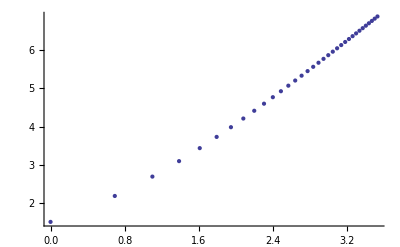

```mathematica
ListPlot[Table[{loglog[[i,1]],loglog[[i,2]]},{i,1,Length[loglog]}]]
```

Using w_i = 1/Δi^2, from Taylor.

```mathematica
weights=Table[1/(loglog[[i,3]]^2),{i,1,Length[loglog]}];
```

This is also from Taylor, used below

```mathematica
Delta=Sum[weights[[i]],{i,Length[weights]}]*Sum[weights[[i]]*loglog[[i,1]]^2,{i,Length[loglog]}]-(Sum[weights[[i]]*loglog[[i,1]],{i,Length[loglog]}])^2;
```

More symbols to make expressions less unweildy.

```mathematica
x[i_]:=loglog[[i,1]];
y[i_]:=loglog[[i,2]];
w[i_]:=weights[[i]];
```

Now, the fit coefficients (for line off form y = A + Bx):

```mathematica
A=1/Delta(Sum[w[i]*x[i]^2,{i,Length[loglog]}]*Sum[w[i]*y[i],{i,Length[loglog]}]-Sum[w[i]*x[i],{i,Length[loglog]}]*Sum[w[i]*x[i]*y[i],{i,Length[loglog]}])
```

0.244328

```mathematica
B=1/Delta(Sum[w[i],{i,Length[loglog]}]*Sum[w[i]*x[i]*y[i],{i,Length[loglog]}]-Sum[w[i]*x[i],{i,Length[loglog]}]*Sum[w[i]*y[i],{i,Length[loglog]}])
```

1.87963

Again, not quite quadratic. We can plot both:

```mathematica
F[x_]:=A+B*x
```

```mathematica
Needs["ErrorBarPlots`"]
```

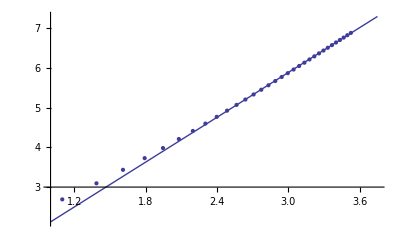

```mathematica
Show[Plot[F[x],{x,1.,3.75}],ErrorListPlot[Table[{{x[i],y[i]},ErrorBar[loglog[[i,3]]]},{i,1,Length[loglog]}]]]
```

Uncertainties in A and B:

```mathematica
σA=Sqrt[Sum[w[i]*x[i]^2,{i,Length[loglog]}]/Delta]
```

0.000102501

```mathematica
σB=Sqrt[Sum[w[i],{i,Length[loglog]}]/Delta]
```

0.0000310214

This is the max value for B:

```mathematica
B+%22
```

{2.07695,1.87963}

Checking the goodness of the fit:

```mathematica
fitvals=Table[F[loglog[[i,1]]],{i,1,Length[loglog]}];
```

```mathematica
residuals=Table[fitvals[[i]]-loglog[[i,2]],{i,1,Length[loglog]}];
```

These look like a curve, not random, which kind of worries me a bit. That said, the fit looks okay.

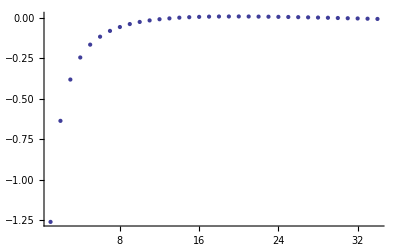

```mathematica
ListPlot[residuals]
```

This expression should output a list of booleans. TRUE means that the fit is inside the error bars (resdiual < error bar) and FALSE means it’s outside

```mathematica
Table[Abs[residuals[[i]]]<loglog[[i,3]],{i,1,Length[loglog]}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

Making sure nothing stupid happened:

```mathematica
fitvals
```

{0.244328,1.54719,2.30932,2.85006,3.26948,3.61218,3.90193,4.15292,4.37431,4.57235,4.7515,4.91505,5.0655,5.20479,5.33447,5.45578,5.56973,5.67717,5.7788,5.87521,5.96692,6.05436,6.13791,6.21791,6.29464,6.36836,6.4393,6.50766,6.57361,6.63734,6.69897,6.75865,6.81649,6.8726}

```mathematica
Table[loglog[[i,2]],{i,1,Length[loglog]}]
```

{1.50487,2.18317,2.68994,3.09435,3.43441,3.72797,3.98189,4.20891,4.412,4.59696,4.76669,4.92293,5.06814,5.20288,5.32979,5.44911,5.56159,5.66821,5.7697,5.86592,5.95794,6.046,6.13016,6.21109,6.28863,6.36343,6.43558,6.50517,6.5724,6.63761,6.70074,6.7617,6.82108,6.87866}

Not...that I can see :( :( :(

## General Quadratic Fit

```mathematica
quadfit=FindFit[Table[final[[i,1]],{i,1,Length[final]}],a x^2 + b x + c, {a,b,c},{x}]
```

{a→0.785389,b→0.0517547,c→0.0578679}

```mathematica
G[x_]:=a x^2 + b x + c /.quadfit
```

```mathematica
quadfitvals=Table[G[i],{i,1,Length[final]}];
```

```mathematica
quadresiduals=Table[quadfitvals[[i]]-final[[i,1]],{i,1,Length[final]}];
```

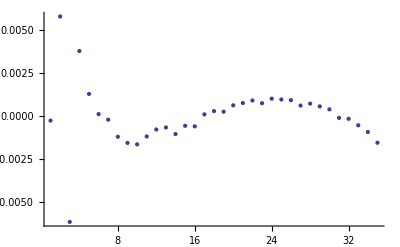

```mathematica
ListPlot[quadresiduals]
```

```mathematica
Table[Abs[quadresiduals[[i]]]<final[[i,2]],{i,1,Length[final]}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}